### Template for making pretty density plots

This notebook contains a basic snippet of code for plotting pretty ContourPlots using Mathematica. 
You can use this to check the behavior of the solution of PDEs. 

I illustrate the code with the example done in the notes, corresponding to the 1D heat equation with (L = 1)

u_0(x) = x (x^2-3x +2)

The general solution is

u(x,t) = ∑_(n =1)^∞  b_n e^(-i α k_n^2 t)sin(k_n x)

where

b_n  = 2/L∫_0^L u_0(x) sin(k_n x) dx

For our example we get (L = 1)

```mathematica
bn = FullSimplify[2 Integrate[x (x^2-3x + 2) Sin[n π x],{x,0,1}],n∈Integers]
```

12/(n^3 π^3)

We now use this to define our solution. We take the sum up to a certain large value nmax.
We then plot the result. Everything else are just cosmetic options for the DensityPlot function, which you can play with if you want (α = 1):

```mathematica
nmax = 300;
sol = Sum[bn Exp[-(n π)^2 t] Sin[n π x],{n,1,nmax}];
```

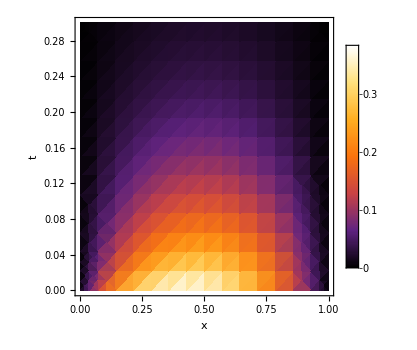

```mathematica
plot=DensityPlot[sol,{x,0,1},{t,0,0.3},
ImageSize->350,
FrameLabel->{"x","t"},
ColorFunction->"SunsetColors",
PlotLegends->Automatic,
PlotRangePadding->None,
PlotRange->All,
LabelStyle->{FontFamily->"Times",20,Black}
]
```

You can also export them as follows

```mathematica
(* Makes the default directory the same as the notebook you are working *)
SetDirectory[NotebookDirectory[]] 

(* Here "plot" is the name I gave to the plot above. *)
Export["MyFig.png",plot,ImageResolution->300];
```

I also recommend that, in the case of Density Plots, you use png instead of PDF. 
PDFs tend to get very heavy.

### Outros exemplos de condições iniciais sugeridos em aula

#### Exemplo do Marcio

```mathematica
bn=FullSimplify[2 Integrate[HeavisideTheta[x-0.4] HeavisideTheta[0.6-x]  Sin[n π x],{x,0,1}],n∈Integers]
```

(0.63662 Cos[1.25664 n]-0.63662 Cos[1.88496 n])/n

```mathematica
nmax = 300;
sol = Sum[bn Exp[-(n π)^2 t] Sin[n π x],{n,1,nmax}];
```

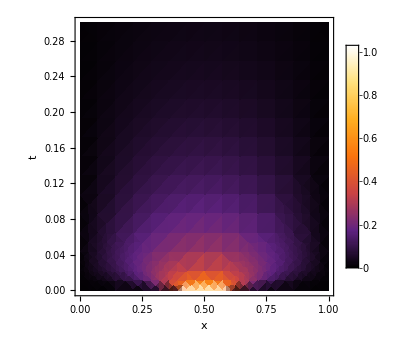

```mathematica
plot=DensityPlot[sol,{x,0,1},{t,0,0.3},
ImageSize->350,
FrameLabel->{"x","t"},
ColorFunction->"SunsetColors",
PlotLegends->Automatic,
PlotRangePadding->None,
PlotRange->All,
LabelStyle->{FontFamily->"Times",20,Black}
]
```

#### Exemplo do Thiago

```mathematica
bn=FullSimplify[2 Integrate[(Sin[10x]+1)  Sin[n π x],{x,0,1}],n∈Integers]
```

2 ((1+(-1)^(1+n))/(n π)+((-1)^(1+n) n π Sin[10])/(-100+n^2 π^2))

```mathematica
nmax = 300;
sol = Sum[bn Exp[-(n π)^2 t] Sin[n π x],{n,1,nmax}];
```

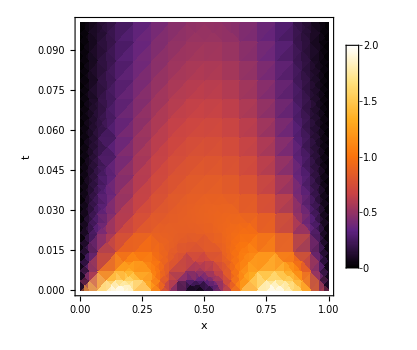

```mathematica
plot=DensityPlot[sol,{x,0,1},{t,0,0.1},
ImageSize->350,
FrameLabel->{"x","t"},
ColorFunction->"SunsetColors",
PlotLegends->Automatic,
PlotRangePadding->None,
PlotRange->All,
LabelStyle->{FontFamily->"Times",20,Black}
]
```

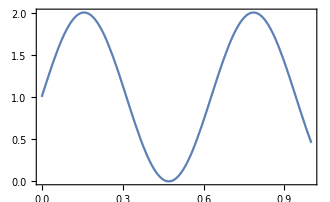

```mathematica
Plot[Sin[10x]+1,{x,0,1}]
```

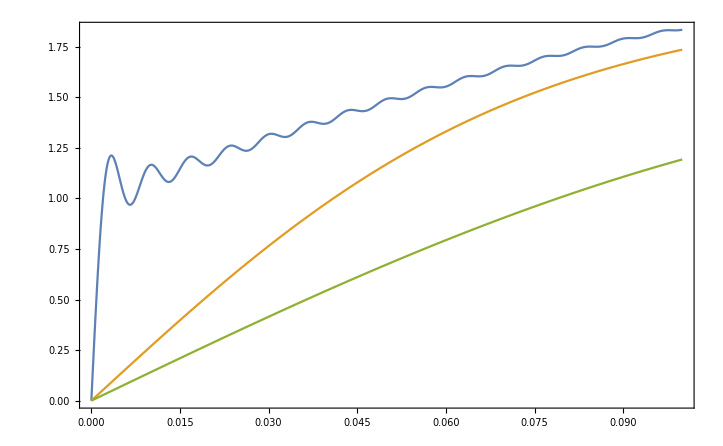

```mathematica
Quiet@Plot[Evaluate@Table[sol,{t,{0,0.001,0.005}}],{x,0,0.1}]
```

#### Exemplo do Luca

```mathematica
bn=FullSimplify[2 Integrate[Exp[-x]  Sin[n π x],{x,0,1}],n∈Integers]
```

(2 ((-1)^(1+n)+ⅇ) n π)/(ⅇ+ⅇ n^2 π^2)

```mathematica
nmax = 300;
sol = Sum[bn Exp[-(n π)^2 t] Sin[n π x],{n,1,nmax}];
```

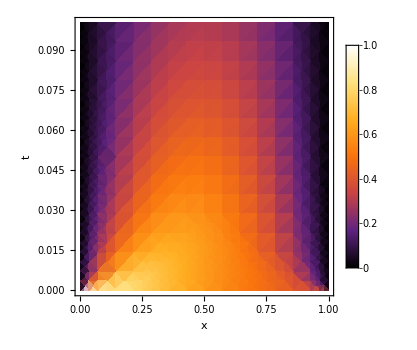

```mathematica
plot=DensityPlot[sol,{x,0,1},{t,0,0.1},
ImageSize->350,
FrameLabel->{"x","t"},
ColorFunction->"SunsetColors",
PlotLegends->Automatic,
PlotRangePadding->None,
PlotRange->All,
LabelStyle->{FontFamily->"Times",20,Black}
]
```

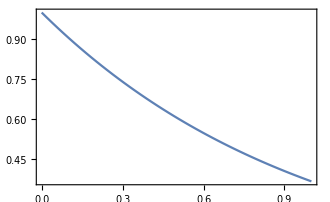

```mathematica
Plot[Exp[-x],{x,0,1}]
```

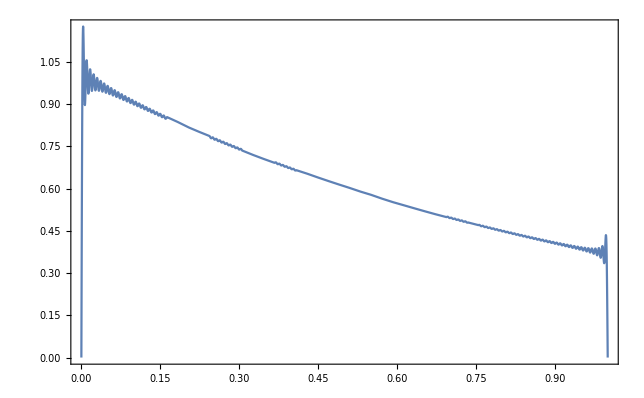

```mathematica
Quiet@Plot[Evaluate@Table[sol,{t,{0(*,0.001,0.005*)}}],{x,0,1}]
```

#### Exemplo do Gabriel

```mathematica
bn=FullSimplify[2 Integrate[1/x  Sin[n π x],{x,0,1}],n∈Integers]
```

2 SinIntegral[n π]

```mathematica
nmax = 300;
sol = Sum[bn Exp[-(n π)^2 t] Sin[n π x],{n,1,nmax}];
```

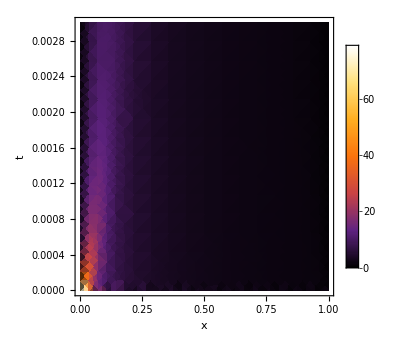

```mathematica
plot=DensityPlot[sol,{x,0,1},{t,0,0.003},
ImageSize->350,
FrameLabel->{"x","t"},
ColorFunction->"SunsetColors",
PlotLegends->Automatic,
PlotRangePadding->None,
PlotRange->All,
LabelStyle->{FontFamily->"Times",20,Black}
]
```

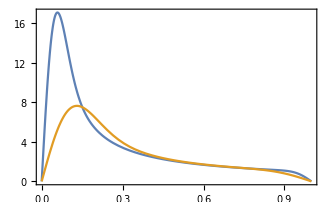

```mathematica
Quiet@Plot[Evaluate@Table[sol,{t,{0.001,0.005}}],{x,0,1}]
```